## Frequencies

### Applying Discrete Fourier Transform

```mathematica
f[x_]:=2Sin[x]+Sin[3x];
xtableRaw=Table[x,{x,0,45,1}];
deg[x_]:=x*π/180;
xtableDeg[data_]:=Map[deg,data];
extra=45;
f2[x_]:=2Sin[x+deg[extra]]+Sin[3x];
```

### Adjust the original function with an additional phase

```mathematica
fadj[x_,a_]:=2Sin[x+a]+Sin[3x];
```

## Graphical representation of the function

```mathematica
mapper[function_,objectdata_]:=Map[function,objectdata];
plotter[function_,data_]:=ListPlot[mapper[function,xtableDeg[data]],Joined->True,Frame->True,Axes->False,PlotStyle->{Red,Thick},FrameStyle->Directive[Black,Thick]];
```

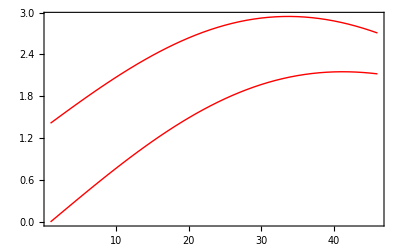

```mathematica
Show[plotter[f,xtableRaw],plotter[f2,xtableRaw],PlotRange->All]
```

## Size of N

```mathematica
Nsize=Length[xtableRaw];
```

### Fourier function (DFT)

```mathematica
dft[N_,n_,k_]:=Exp[-2π*ⅈ*n*k/N];
```